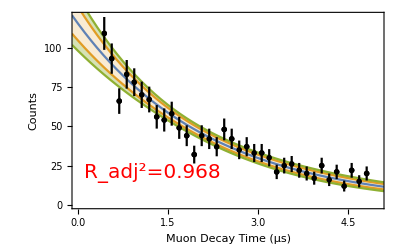

```mathematica
Needs["ErrorBarPlots`"]
data=Import[NotebookDirectory[]<>"Mathematica_format.txt","Table"];
errors = Table[√data[[i,2]],{i,1,Length[data]}];
errorbars = Table[ErrorBar[errors[[i]]],{i,1,Length[data]}];
ziperrorbardata = MapThread[List,{data,errorbars}];
weights = Table[1/errors[[i]]^2,{i,1,Length[data]}];
model = a ⅇ^(-t/τ);
nlm =NonlinearModelFit[data,model,{a,τ},t, Weights->weights];
sols = nlm["BestFitParameters"];
bestfit = model/.sols;
τuncertainty = Round[nlm["ParameterErrors"][[2]],0.01];
radjsquared = Round[nlm["AdjustedRSquared"],0.001];
{bands90[t_],bands95[t_],bands99[t_]} = Table[nlm["MeanPredictionBands", ConfidenceLevel->conf],{conf,{0.90,0.95,0.99}}];

marker = Graphics[{Black, Disk[]}];
legendstyle = Directive[FontFamily->"Arial",Black,FontSize->10];

plot1=ListPlot[data,PlotMarkers->{marker, 0.025}, PlotLegends->Placed[{"Data"},{Right, Top}], LabelStyle->legendstyle];
plot2 = Plot[{nlm[t],bands90[t],bands99[t]},{t,-0.1,5.1},Filling->{2->{1},3->{2}},PlotLegends->Placed[{"Best Fit τ="<>ToString[Round[(τ/.sols),0.01]]<>"±"<>ToString[τuncertainty]<>" μs","90% Confidence Level","99% Confidence Level"},{Right,Top}],LabelStyle->legendstyle, PlotRange->{{0,5},{-250,300}}];
plot3 = ErrorListPlot[ziperrorbardata, PlotMarkers->{marker,0.025}, PlotStyle->Black];
text = Text[Style["R_adj^2="<>ToString[radjsquared],Red,20],{0.1,20},{-1,0}];
textgfx = Graphics[text];
finalplot=Show[plot1,plot2,plot3,textgfx,FrameLabel->{{"Counts",""},{"Muon Decay Time (μs)",""}},Frame->True, PlotRange->{{0,5},{0,120}}]
Export[NotebookDirectory[]<>"MuonLifetimePlot.svg",finalplot, "SVG"];
Export[NotebookDirectory[]<>"MuonLifetimePlot.png",finalplot, "PNG"];
```